# Colorful Fraud: Utilizing Adversarial Examples to Expose Vulnerabilities in Neural Network Architectures

## Wolfram Summer Camp 2019

Nico Adamo, Philip Maymin

In a day and age where many consider deep learning an off-the-shelf solution to any and all classification/prediction problems, it’s important that people examine whether their neural network models are vulnerable to targeted attacks. This project focuses on implementing a framework for generating ‘adversarial examples’: examples which expose unexpected behavior in the results of the neural network. Such a task is split into two applications: generating what should be easily-classifiable inputs that fool the neural network, and generating random-looking inputs that return targeted, high-probability results when fed to the neural network. We implement the Fast Gradient Sign Method (Goodfellow 2014b) for the former, and an original algorithm modeled after FGSM for the latter. Using these algorithms, we examine whether these adversarial examples are in fact edge cases, or make up a majority of the neural network’s classification space. We also construct two methods for trying to minimize adversarial examples, and evaluate their accuracy at detecting and overcoming adversarial images.

## An Introduction to Adversarial Examples

### What is an adversarial example?

Let’s look at a neural network trained to identify images - VGG-16:

```mathematica
imageIdentify=NetModel["VGG-16 Trained on ImageNet Competition Data"];
```

This network is state-of-the-art in terms of image identification, giving us very good results for almost all images:

```mathematica
imageIdentify[-Graphics-,"TopProbabilities"]
```

{giant panda→0.999966}

...almost.

```mathematica
imageIdentify[-Graphics-,"TopProbabilities"]
```

{indri→0.608596,colobus→0.0884141,lar gibbon→0.0838024,ring-tailed lemur→0.0786162}

That second image is not the same! It is in fact different, by very slight pixel values. Normally, neural networks are resilient to things like changing brightness, even hue. But we can execute a targeted attack to make the smallest (mathematically optimal) perturbation to the image to maximize the “wrongness” of it’s output.
In a similar vein, let’s try this:

```mathematica
imageIdentify[-Graphics-,"TopProbabilities"]
```

{giant panda→0.999919}

Just a blank image? Well, let’s increase the brightness:

```mathematica
ImageAdjust[-Graphics-,{0,9}]
```

-Graphics-

And suddenly, a whole network of structure reveals itself. This is the concept of an “adversarial example”: something crafted to cause the neural network to produce unexpected, or even uncontrolled, behavior.

## Creation, Calculation, and Counteraction

### Generating adversarial examples

#### Image Perturbation (FGSM)

For adversarial images of the type of the first example above, we implement the Fast Gradient Sign Method (FGSM). This is an algorithm, originally described by Goodfellow (2014) that makes the smallest possible change to an image to maximize the loss function of the neural network - in this case, categorical cross entropy.   It does this by calculating the sign of the gradient of the loss function with respect to the input. What this gives is effectively an image representing how much changing each RGB value in the image effects the returned probability overall.

```mathematica
imageAdversarialPerturbed[sourceImg_,net_,epsilon_]:= With[{
		lossNet=NetChain[{
			NetReplacePart[net,{"Output" -> None}], 
			AggregationLayer[Max,1], 
			ElementwiseLayer[-Log[#]&]
		}],
		encoder=NetExtract[net,"Input"]
	},
	ImageResize[NetDecoder[encoder][encoder[sourceImg]+epsilon*Sign[lossNet[sourceImg,NetPortGradient["Input"]]]],ImageDimensions@sourceImg]]
```

This function takes in a sourceImage, which is your initial image, a neural network that you are maximizing the loss of, and a factor “epsilon” representing how far you move along the gradient. Higher values of epsilon correspond to larger changes, but to get more accurate results, it is recommenced to Nest imageAdversarialPerturbed with a smaller value of epsilon so that you re-calculate the gradient at each step. 

This function first defines a neural network “lossNet” that is made up of net up to it’s softmax layer, an AggregationLayer that takes the maximum probability returns, and then an ElementwiseLayer that calculates the -Log of that value to get the loss. It is necessary to define this as a neural network to be able to calculate the gradient. Since the gradient of a neural network works on the encoded input array, we add the gradient to the encoded input, and then invert the encoder.  Let’s try some examples:

```mathematica
-Graphics-->imageIdentify[-Graphics-,"TopProbabilities"]
perturbedEx1=imageAdversarialPerturbed[-Graphics-,imageIdentify,0.01];
perturbedEx1->imageIdentify[perturbedEx1,"TopProbabilities"]
```

-Graphics-→{lemon→0.990056}

-Graphics-→{rock beauty→0.404247,jackfruit→0.167216,knee pad→0.0572218}

```mathematica
-Graphics-->imageIdentify[-Graphics-,"TopProbabilities"]
perturbedEx1=imageAdversarialPerturbed[-Graphics-,imageIdentify,0.01];
perturbedEx1->imageIdentify[perturbedEx1,"TopProbabilities"]
```

-Graphics-→{pizza→0.942703}

-Graphics-→{honeycomb→0.960892}

Try some of your own, and see what kind of results you get!

#### Targeted Adversarial Examples

Here, we introduce a new algorithm for perturbing images, not away from high-probability, but towards high-probability of a certain class. This is done by somewhat reversing the process of FGSM, with respect to a slightly different neural network. We define our loss function like normal categorical cross entropy, but “fake” the assigned label such that it is probability 1 for whatever class we decide, and 0 for all others. Then, we perform gradient descent, not on the weights of the network, but on the input pixels of the image, using this “fake loss” function. With very small step size, repeating this process guarantees an optimal path to the ‘nearest’ image with high-confidence for a certain class. Here is this algorithm implemented in Mathematica:

```mathematica
ClearAll[imageAdversarialTargeted]
imageAdversarialTargeted[sourceImg_Image, net_, epsilon_, maxLayer_: None, maxSteps_ : 15] := With[{
		lossNet = NetChain[{
			NetReplacePart[net, {"Output"->None}],
			If[maxLayer===None,
				AggregationLayer[Max, 1],
				PartLayer[maxLayer]],
				ElementwiseLayer[-Log[#]&]
				}],
		encoder = NetExtract[net,"Input"]
	},
	ImageResize[Nest[NetDecoder[encoder][encoder[#]-epsilon*Sign[lossNet[#,NetPortGradient["Input"]]]]&,sourceImg,maxSteps],ImageDimensions@sourceImg]]
```

The PartLayer in this function takes the class with maxIndex from the softmax of the network. If we maximize with respect to class “-1”, it will travel to the nearest high-probability image of any class, by traveling towards it’s current highest probability. For convenience, here are some helper functions for this algorithm:

```mathematica
ClearAll[genImageIdentifyNet,blankImage,visualizeImage,classFromNumber,numberFromClass,classSearch]
genImageIdentifyNet[sizeMult_]:=With[{
		imageIdentify=NetModel["VGG-16 Trained on ImageNet Competition Data"]
	},
	NetJoin[NetReplacePart[NetAppend[NetTake[imageIdentify,"pool5"],"downPooling"->PoolingLayer[{sizeMult,sizeMult},{sizeMult,sizeMult}]],"Input"->NetEncoder[{"Image",224*sizeMult}]],NetTake[imageIdentify,{"flatten_0","prob"}]]]
blankImage[color_,size_]:=Image@ConstantArray[color,size]
visualizeImage[img_,net_,bright_ : 10]:=ImageAdjust[img,{0,bright}]->net[img,"TopProbabilities"]
classFromNumber[net_,num_]:=NetExtract[net,"Output"][["Labels"]][[num]]
numberFromClass[net_,class_]:=Flatten@Position[NetExtract[net,"Output"][["Labels"]],class]//First
classSearch[net_,str_]:=Select[MapIndexed[{#2[[1]],#1}&,NetExtract[net,"Output"][["Labels"]]],StringContainsQ[CommonName[#[[2]]],str,IgnoreCase->True]&]
```

genImageIdentifyNet generates a version of Image Identify that, instead of instantly squishing images to 224x224, works with images of 224xsizeMult. Note, since pooling is done at the end of the network to retain detail, genImageIdentifyNet[n>5] can be very slow and computationally intensive. 
visualizeImage increases the brightness of an image and shows it’s results in the neural network provided, with an optional brightness argument. 
classSearch allows you to search for a string and get the class index of that string in whatever neural net you provide, necessary because imageAdversarialTargeted takes class index, rather than an entity.

Let’s try some examples:

```mathematica
visualizeImage[imageAdversarialTargeted[RandomImage[0.1,{400,400},ColorSpace->"Grayscale"],imageIdentify,0.01,106,16],imageIdentify,5](*106 is the index of koala*)
```

-Graphics-→{koala→1.}

```mathematica
visualizeImage[imageAdversarialTargeted[blankImage[{0,0,0},{300,300}],imageIdentify,0.01,45,16],imageIdentify](*45 is the index of alligator*)
```

-Graphics-→{alligator lizard→1.}

```mathematica
visualizeImage[imageAdversarialTargeted[-Graphics-,imageIdentify,0.01,270,7],imageIdentify,0]
```

-Graphics-→{gray wolf→0.932666}

This process works with any softmax neural network, and can be easily extended to non-softmax neural networks. Let’s look at ageIdentify, a neural network made to identify ages from pictures. Notice that we get more definite features from a network trained on more similar data, leading to objectively terrifying results:

```mathematica
ageIdentify=NetModel["Age Estimation VGG-16 Trained on IMDB-WIKI and Looking at People Data"];
visualizeImage[imageAdversarialTargeted[blankImage[{0,0,0},{300,300}],ageIdentify,0.01,10],ageIdentify]
```

-Graphics-→{9→0.371486,7→0.182983,0→0.161642,8→0.140831,10→0.0802514}

Can our age targeting function act as a fountain of youth? Let’s try it:

```mathematica
{-Graphics-,visualizeImage[imageAdversarialTargeted[-Graphics-,ageIdentify,0.01,10,7],ageIdentify,0]}
```

{-Graphics-,-Graphics-→{9→0.379493,7→0.177606,8→0.136737,10→0.131657,11→0.0742032}}

I’m definitely feeling the youthful energy.

### Measuring statistics

So just how bad is the problem of adversarial examples? Well, let’s create a function to sample from the space of random images and check the top probability given by Image Identify, and create a distribution of the most common probabilities:

```mathematica
getProbSize[size_,sample_]:=Monitor[Table[imageIdentify[RandomImage[1,size,ColorSpace->"RGB"],"TopProbabilities"->1][[1]][[2]],{n,1,sample}],n]
```

Now let’s see the probabilities for certain sizes of images (100x100, 200x200, 300x300, 400x400) (this will take about 15 minutes):

```mathematica
advStats=Table[getProbSize[{s,s},400],{s,100,400,100}];
```

And we can look at histograms for the data:

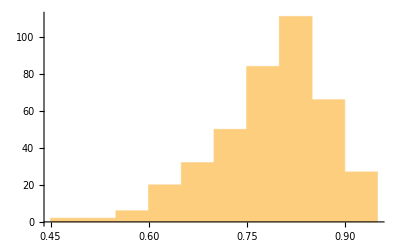
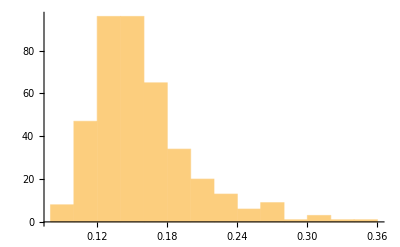
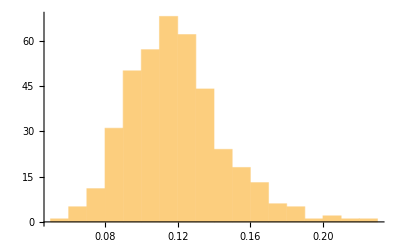
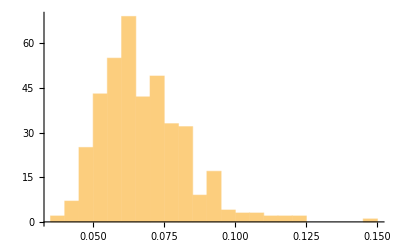

```mathematica
Histogram/@advStats
```

100x100 exists on the very boundary of an image space that is small enough to be made up in significant part by adversarial examples. This phenomena peaks at 80x80, where almost all images are adversarial to imageIdentify. Below that, images are too small to get many high-probability results. Above 100x100, there is a very sharp drop off in average probability. From this data, we can model the distribution of advStats and find the probability that any given random image will have be classified with high-confidence (>0.9) by the neural network:

```mathematica
dist=FindDistribution/@advStats;
MapThread[#1->#2&,{{100,200,300,400},Probability[x>0.9,x\[Distributed]#]&/@dist}]
```

{100→0.062411,200→3.0244×10^-11,300→6.24372×10^-21,400→0}

The percentage of our image space made up of high-confidence images gets incredibly small, but the absolute amount of images is actually much bigger. Here’s the difference between the amount of 300x300 high-confidence images and 100x100 high-confidence images.

```mathematica
6.243718*10^-21*(256)^(300*300)-0.062411*(256)^(100*100)
```

2.46786470154789×10^216721

But how many of the high confidence images are real, correctly-classified images, and how many are adversarial examples?  To find out, we can sample from the space of high-confidence images and see how many are also high-confidence with respect to another neural network, trained on a different dataset and with a different structure. This radically differing structure confirms that there will be no transfer of adversarial examples between the two nets (Goodfellow 2014b, Szgedy et al). First, let’s load in an external neural network and write a function to sample randomly from the space of adversarial examples, using our targeted FGSM attack on a random image:

```mathematica
im2=NetModel["Wolfram ImageIdentify Net V1"]
generateAdversarial[size_]:=imageAdversarialTargeted[RandomImage[1,size,ColorSpace->"RGB"],imageIdentify,0.01,-1,3]
```

Let’s refer to the neural network for which we are constructing adversarial examples our “victim net”.  We next construct a function that takes an image size and sample size, and returns a list of measures of adversality, determined by the victim net’s probability minus our external neural networks probability. The higher adversality, the more we’ve fooled our victim net. Let’s make a histogram of adversality for 100x100 images, and calculate the probability that an image is correctly classified, meaning the difference between the two networks classifications is less than 10%:

```mathematica
advReal[size_,sample_]:=
```

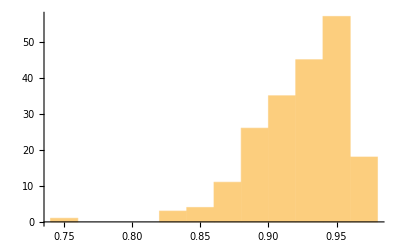

1.70154×10^-34

```mathematica
Histogram@advVsreal
prob=FindDistribution[advVsreal];
Probability[x<0.1,x\[Distributed]prob]
```

In fact, this number is probably a gross overestimate, seeing as this difference does not require our external and victim net to classify things in the same class - however, it is impossible to adjust for this because the classes of the two nets are not the same. In other words, the number of real images is almost negligible. Try repeating this experiment for 400x400 and even 800x800 images: you’ll find the same result. Putting all of this together, we have learned a few things:

The space of high-confidence results of image-identification neural networks is incredibly vast, although very small in proportion to the space of random images overall

The vast majority of high-confidence results are adversarial examples, with the number of real images being pretty much insignificant.

#### Brittleness measurements

We can also measure how “brittle” these targeted adversarial examples are, in comparison to normal test images. The normal heuristic for this case would be to use noise to determine how sensitive the images are to changes: however, this doesn’t work because our neural network interprets our DeepDream-esque adversarial examples + noise as “maze” almost always, leaving us effectively “circling the drain” of adversarial examples. Instead, we use the reverse process of our targeted adversarial attack to try to get away from high probabilities as fast as possible. Since this process is optimal, this gives us a realistic view of the size of our “high-probability cluster” in the space of images.   

First, we define a function that performs gradient ascent to get away from high-confidence measurements, and counts the number of steps. This code is very similar to the above code for imageAdversarialTargeted, so we won’t review it here:

```mathematica
Clear[countNumUntilNotConfident]
countNumUntilNotConfident[img_,net_,epsilon_,cutoff_]:=Module[{i=0,lossNet=NetChain[{NetReplacePart[net,{"Output"->None}],AggregationLayer[Max,1],ElementwiseLayer[-Log[#]&]}],encoder=NetExtract[net,"Input"]},NestWhile[(i++;NetDecoder[encoder][encoder[#]+epsilon*Sign[lossNet[#,NetPortGradient["Input"]]]])&,img,imageIdentify[##,"TopProbabilities"][[1]][[2]]>cutoff&];i]
```

Next, we get some adversarial examples:

```mathematica
advList=Iconize[imageAdversarialTargeted[RandomImage[1,{400,400},ColorSpace->"RGB"],imageIdentify,0.01,-1,6]&/@Range[20]]
```

We then see how many steps it takes until these images are no longer high-confidence:

```mathematica
confidenceStepsAdv=countNumUntilNotConfident[#,imageIdentify,0.01,.5]&/@advList[[1]]
```

{2,1,1,4,6,3,16,6,6,5,7,6,1,3,6,7,14,1,3,1}

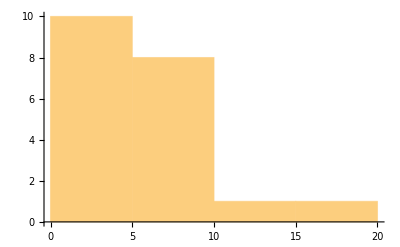

```mathematica
Histogram[confidenceStepsAdv]
```

Next, we repeat this for real images:

```mathematica
realImages=;
confidenceStepsReal=countNumUntilNotConfident[#,imageIdentify,0.01,.5]&/@(ImageResize[#,400]&/@realImages[[;;30]])
```

{1,1,3,3,1,2,4,3,2,6,2,3,4,1,3,2,5,1,1,2,4,2,1,2,4,1,1,1,2,2}

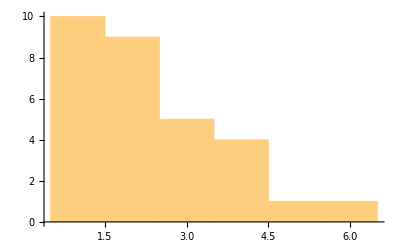

```mathematica
Histogram@confidenceStepsReal
```

So it seems that adversarial examples are in fact much harder to escape from than real images, and are much more robust to changes than normal images by a factor of more than double.

### Beating adversarial examples

So how do we beat adversarial examples? It seems like an uphill battle when you can mathematically optimize loss of any neural network, even those trained to recognize adversarial examples - especially because, as we’ve shown, the space of adversarial examples is much bigger than the space of real images so trying to train the network on enough adversarial examples to make a difference will wash out the original dataset.

#### The DPRK Method

But let's think back to our statistical analysis, and how we detected adversarial examples vs real images: we used a different neural network to verify the results of the other. This leads us to a process (henceforth) known as the "democratic probabilistic reasoning kernel", or "DPRK". DPRK uses a collection of neural networks trained on the same architecture but initialized differently and averages their softmax layers to get the final probability vector. It takes advantage of an as-of-yet unexplained property of adversarial examples for different neural networks with similar architecture: they are transferable, but give different results. This means that high-confidence adversarial examples for one neural network give high-confidence results for another neural network, but it will be high-confidence for a different class. When the architectures are exactly the same, this phenomenon stretches to the extreme - moving the gradient of one neural network in the direction of a class C moves the gradient of the other neural network in the direction of a different class D by the exact same magnitude. 

The result of this is that adversarial examples get "stuck" between neural networks. When it tries to optimize the gradient of one, it de-optimizes the gradient of another. The best, therefore, that the neural network can do is to split probabilities evenly between the neural network: so if we have 5 neural networks, it will gives a probability vector with 5 elements with 0.2 probability. 

In practical application, it is still possible to generate adversarial images with this. This is because it is possible for multiple of the neural networks to happen to travel in the same direction - but this happens by random chance, and cannot be predicated or optimized because the mechanism of this adversarial transfer is unexplained. So, this scales the difficulty of generating adversarial networks by C^n, where C is your number of classes and n is your number of neural networks. Using 10 ImageIdentify networks, what is a 6-second process on my laptop would take 2 * 10^23 years, by which time my computer will have become, as they say, dust in the wind. Let's implement a toy model of DPRK for MNIST digits:

First, let’s construct a robust MNIST ConvNet for testing purposes, following both the Wolfram and TowardsDataScience spec:

```mathematica
resource=ResourceObject["MNIST"];
trainingData:=ResourceData[resource,"TrainingData"];
trainData[]:=RandomSample[trainingData][[;;30000]];
testData=ResourceData[resource,"TestData"];
lenet=NetChain[{ConvolutionLayer[20,5],Ramp,PoolingLayer[2,2],ConvolutionLayer[50,5],Ramp,PoolingLayer[2,2],FlattenLayer[],500,Ramp,10,SoftmaxLayer[]},"Output"->NetDecoder[{"Class",Range[0,9]}],"Input"->NetEncoder[{"Image",{28,28},"Grayscale"}]]
```

NetChain[<>]

Next, let’s train it:

```mathematica
lenet=NetTrain[lenet,trainingData,ValidationSet->testData,MaxTrainingRounds->5];
```

And generate an adversarial examples:

```mathematica
imageAdversarialTargeted[blankImage[{0,0,0},{40,40}],lenet,0.01,7,300]
```

-Graphics-

```mathematica
lenet[%,"TopProbabilities"]
```

{6→1.}

Great, working as intended. Now, let’s get a list of 5 neural networks with the same architecture, initialized with different random weights.

```mathematica
leNets=Table[NetTrain[NetInitialize[NetChain[{ConvolutionLayer[20,5],Ramp,PoolingLayer[2,2],ConvolutionLayer[50,5],Ramp,PoolingLayer[2,2],FlattenLayer[],500,Ramp,10,SoftmaxLayer[]},"Output"->NetDecoder[{"Class",Range[0,9]}],"Input"->NetEncoder[{"Image",{28,28},"Grayscale"}]],Method->"Random",RandomSeeding->Automatic],trainingData,ValidationSet->testData,MaxTrainingRounds->4],{n,1,5}]
```

{NetChain[<>],NetChain[<>],NetChain[<>],NetChain[<>],NetChain[<>]}

Chop off all of their net decoders so that we only have softmax output, name each network, and put them in a NetGraph to catenate them and average them:

```mathematica
leNetsSoft=Table["leNet"<>ToString[n]->(NetReplacePart[#,"Output"->None]&/@leNets)[[n]],{n,Length[leNets]}];
```

```mathematica
finalNet=NetGraph[Flatten@{leNetsSoft,"join"->CatenateLayer[],"j"->ReshapeLayer[{5,10}],"agg"->AggregationLayer[Mean,1]},{#->"join"&/@Keys[leNetsSoft],"join"->"j","j"->"agg"}]
finalNetDecode=NetReplacePart[finalNet,"Output"->NetExtract[lenet,"Output"]]
```

NetGraph[<>]

NetGraph[<>]

We can see that our adversarial example above transfers to these other neural networks, but in different ways:

```mathematica
leNets[[1]][-Graphics-,"TopProbabilities"]
leNets[[2]][-Graphics-,"TopProbabilities"]
leNets[[3]][-Graphics-,"TopProbabilities"]
```

{4→1.}

{6→1.}

{8→1.}

So when we try to optimize an adversarial example for our final net, it is forced to split probabilities evenly between the different nets. Note that for most applications, to an attacker the neural network is a “black box”, so this attack is the most realistic example of what an adversarial attack for this neural network would look like:

```mathematica
attack=imageAdversarialTargeted[blankImage[{0,0,0},{40,40}],finalNetDecode,0.01,2,300];
ImageAdjust[attack,{0,100}]
finalNetDecode[attack,"TopProbabilities"]
```

-Graphics-

{8→0.2,5→0.2,3→0.2,2→0.2,1→0.2}

Try an attack with a random image, and you’ll soon see that even this toy example never gives high probability results for adversarial examples. And yet, we lose almost no accuracy on real digits (in fact, for the few times this experiment has been done, often the average net has better probability than the original):

```mathematica
ClassifierMeasurements[lenet,testData,"Accuracy"]
ClassifierMeasurements[finalNetDecode,testData,"Accuracy"]
```

0.9893

0.9795

We can also use our above statistics to try to explain why these adversarial examples transfer across networks with different weights. The goal of a neural network is to generalize - and this is a task, as we know, that they do quite well. Therefore, while the weights of two dissimilar neural networks trained for the same task might be completely differently, by nature  of the effectivity of neural networks, they “carve out” very similar subspaces of the space of images for high-probability classification.  However, these similarities are global, not local: the neural networks learn similar features, i.e. clusters of similar feature vectors “generalized” from the training data, rather than the exact same images. One might expect adversarial examples to be of the latter variety: existing in fine pockets distributed homogeneously through the space of images. However, our “brittleness” measure in fact shows the opposite: it takes many more optimal steps  away from an adversarial example to get to a non-high-probability image than normal, everyday images. This suggests that adversarial examples are in fact clustered more than normal images. One could argue, therefore, that ‘adversarial subspaces’ are the most global features of neural networks. Since dissimilar neural networks trained on the same class are designed to learn global features, this suggests why adversarial examples transfer.

#### Direct Adversarial Training

We can also attempt to create a “shielding” neural network that filters out adversarial examples before they make it to the main neural network. Whereas machine-learning based directly on user input have to get some input and give some output in the frontend, and are therefore vulnerable to adversarial examples, this filter can act completely server-side and therefore not be accessible by the user. By gathering adversarial examples for one neural network, we can train a new neural network that classifies whether a certain image is or is not adversarial to the network it shields. First, we define a function to generate training data:

```mathematica
ClearAll[generateAdversarialTrainingData]
generateAdversarialTrainingData[net_,num_,iter_,OptionsPattern[]]:=With[{
		imageSize=NetExtract[NetExtract[net,"Input"],"ImageSize"],
		colorSpace=NetExtract[NetExtract[net,"Input"],"ColorSpace"] 
	},
	]
	Options[generateAdversarialTrainingData]={Method->"RandomTargeted"}
```

{Method→RandomTargeted}

This function takes a neural network, the number of adversarial examples, how refined the adversarial examples are, and an option Method which  specifies whether each example should target a random class or target no class at all. Using this function to synthesize our training data, along with the normal training data for our neural network, we can make a function to generate a shield net that classifies adversarial examples. The same base architecture as the original network is used, because the adversarial transfer phenomenon discussed above suggests that whatever makes adversarial examples ‘special’ to the original net also works for any net of the same architecture, and therefore we have a better chance of classifying that feature with the same architecture.

```mathematica
genShield[net_,normalTraining_,adversarialTraining_,rounds_]:=With[{
		shieldNet=NetReplacePart[NetJoin[NetDrop[net,-1],{LinearLayer[2],SoftmaxLayer[]}],"Output"->NetDecoder[{"Class",{True,False}}]]
	},
	NetTrain[shieldNet,Join[#->False&/@normalTraining,#->True&/@adversarialTraining],ValidationSet->Scaled[0.1],MaxTrainingRounds->rounds]]
```

Once you have your shield saved, you can use the “shieldNet” function below to filter out adversarial examples, giving $Defended for identified adversarial examples:

```mathematica
shieldNet[shield_,net_,input_]:=If[shield[input]==True,$Defended,net[input]]
```

Let’s test it! First, we generate 10000 adversarial images for our lenet defined above:

```mathematica
dataAdv=generateAdversarialTrainingData[lenet,10000,15]
trainingDataAdvBin=#[[1]]->"NotAdversarial"&/@trainingData;
testDataAdvBin=#[[1]]->"NotAdversarial"&/@testData;
```

And then get a shield from it:

```mathematica
mnistShield=genShield[lenet,Keys@trainingData,dataAdv,1]
```

NetChain[<>]

Let’s now generate a bunch of adversarial examples on lenet:

```mathematica
advExamples=imageAdversarialTargeted[RandomImage[1,{28,28}],lenet,0.01,#,50]&/@Range[10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Finally, let’s feed them through the shield.

```mathematica
shieldNet[mnistShield,lenet,#]&/@advExamples
```

{$Defended,$Defended,$Defended,$Defended,$Defended,$Defended,$Defended,$Defended,$Defended,$Defended}

Put in function repository
Various image processing to measure adversality**
Can you localize the area for which you are changing?** (Designs for T shirts to mess up person recognition)
Rotated MNIST